## grow-example.nb

Example Cellzilla2D notebook illustrating: 
	grow
	SimAnimate
	LineageAnimate
Portions of this notebook’s output have been suppressed (removed) to save space for internet display. All of the input cells included are sufficient to recover the output shown. 

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
```

xCellerator 0.95 (28-Feb-2014) loaded Sat 10 Jun 2017 13:10:26
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51d (10 June 2017)) loaded Sat 10 Jun 2017 13:10:27
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
$HistoryLength=1 (* reduce memory leak *)
```

1

### Generate A Template of 8 cells

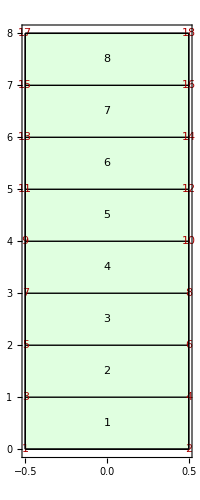

```mathematica
q=TemplateRectangular[{-1/2,1/2,1}, {0,8, 1}];
Q=Tissue2DTissue[q];
ShowTissue[Q,Frame-> True, "CellNumbers"-> True, "VertexNumbers"-> True]
```

### Define an internal pressure gradient in the template with the maximum in the second cell from the top and distributed via a bell curve

```mathematica
TC=Centroid[Q];
top=TissueVertices[Q][[18]];
f[i_]:=X[i]-> (BellCurve[1,top[[2]]-1.5,1.5][TC[[i,2]]]);
```

```mathematica
network={{∅->X,BellCurve[1, tip[2][t]-1.5,1.5][ycen[t]]}, {X-> ∅, 1}};
n=NTissueCells[Q];
centroids=Centroid[Q];
```

```mathematica
myic=f/@Range[n]
```

{X[1]→0.000335463,X[2]→0.00386592,X[3]→0.0285655,X[4]→0.135335,X[5]→0.411112,X[6]→0.800737,X[7]→1.,X[8]→0.800737}

### run the simulation for 25,000 time units

simdir = /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0001.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:29
Memory in Use (GB):  | 0.116111
Max Memory Used (GB):  | 0.13023
Free Memory (GB):  | 0.0755005

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 5 (static cell 5) divides at t = 25.6872

Cell 6 (static cell 6) divides at t = 25.6872

Cell 8 (static cell 8) divides at t = 25.6872

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0002.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:34
Memory in Use (GB):  | 0.122922
Max Memory Used (GB):  | 0.138391
Free Memory (GB):  | 0.0317993
CPU Used(seconds):  | 4.99551
Number of Cells:  | 11
Cell Divisions:  | 3
Simulator Steps:  | 2
Number of Variables:  | 237

Cell Division Errera's Method

Cell 3 (static cell 3) divides at t = 277.718

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0003.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:37
Memory in Use (GB):  | 0.126218
Max Memory Used (GB):  | 0.141691
Free Memory (GB):  | 0.0239601
CPU Used(seconds):  | 8.94757
Number of Cells:  | 12
Cell Divisions:  | 4
Simulator Steps:  | 3
Number of Variables:  | 321

Cell Division Errera's Method

Cell 7 (static cell 7) divides at t = 996.821

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0004.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:42
Memory in Use (GB):  | 0.129072
Max Memory Used (GB):  | 0.144549
Free Memory (GB):  | 0.0252495
CPU Used(seconds):  | 13.7467
Number of Cells:  | 13
Cell Divisions:  | 5
Simulator Steps:  | 4
Number of Variables:  | 349

Cell Division Errera's Method

Cell 10 (static cell 10) divides at t = 1920.94

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0005.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:47
Memory in Use (GB):  | 0.13149
Max Memory Used (GB):  | 0.146971
Free Memory (GB):  | 0.026947
CPU Used(seconds):  | 18.7695
Number of Cells:  | 14
Cell Divisions:  | 6
Simulator Steps:  | 5
Number of Variables:  | 377

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 2892.45

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0006.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:52
Memory in Use (GB):  | 0.134072
Max Memory Used (GB):  | 0.149556
Free Memory (GB):  | 0.0232086
CPU Used(seconds):  | 24.6363
Number of Cells:  | 15
Cell Divisions:  | 7
Simulator Steps:  | 6
Number of Variables:  | 405

Cell Division Errera's Method

Cell Division Errera's Method

Cell 2 (static cell 2) divides at t = 3953.22

Cell 11 (static cell 11) divides at t = 3953.22

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0007.png

Actual Clock Time:  | 10-Jun-2017-at-13:11:59
Memory in Use (GB):  | 0.136116
Max Memory Used (GB):  | 0.151607
Free Memory (GB):  | 0.0276756
CPU Used(seconds):  | 32.3649
Number of Cells:  | 17
Cell Divisions:  | 9
Simulator Steps:  | 7
Number of Variables:  | 433

Cell Division Errera's Method

Cell 4 (static cell 4) divides at t = 4674.25

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0008.png

Actual Clock Time:  | 10-Jun-2017-at-13:12:06
Memory in Use (GB):  | 0.138971
Max Memory Used (GB):  | 0.154466
Free Memory (GB):  | 0.0239258
CPU Used(seconds):  | 39.1768
Number of Cells:  | 18
Cell Divisions:  | 10
Simulator Steps:  | 8
Number of Variables:  | 489

Cell Division Errera's Method

Cell 7 (static cell 7) divides at t = 4819.44

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0009.png

Actual Clock Time:  | 10-Jun-2017-at-13:12:13
Memory in Use (GB):  | 0.141328
Max Memory Used (GB):  | 0.156828
Free Memory (GB):  | 0.0235481
CPU Used(seconds):  | 46.5201
Number of Cells:  | 19
Cell Divisions:  | 11
Simulator Steps:  | 9
Number of Variables:  | 517

Cell Division Errera's Method

Cell 6 (static cell 6) divides at t = 6527.45

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0010.png

Actual Clock Time:  | 10-Jun-2017-at-13:12:20
Memory in Use (GB):  | 0.14599
Max Memory Used (GB):  | 0.161492
Free Memory (GB):  | 0.0265999
CPU Used(seconds):  | 54.4228
Number of Cells:  | 20
Cell Divisions:  | 12
Simulator Steps:  | 10
Number of Variables:  | 545

Cell Division Errera's Method

Cell Division Errera's Method

Cell 1 (static cell 1) divides at t = 8884.11

Cell 8 (static cell 8) divides at t = 8884.11

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0011.png

Actual Clock Time:  | 10-Jun-2017-at-13:12:29
Memory in Use (GB):  | 0.150243
Max Memory Used (GB):  | 0.165754
Free Memory (GB):  | 0.0277328
CPU Used(seconds):  | 63.8038
Number of Cells:  | 22
Cell Divisions:  | 14
Simulator Steps:  | 11
Number of Variables:  | 573

Cell Division Errera's Method

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 9237.08

Cell 15 (static cell 15) divides at t = 9237.08

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0012.png

Actual Clock Time:  | 10-Jun-2017-at-13:12:40
Memory in Use (GB):  | 0.15285
Max Memory Used (GB):  | 0.172796
Free Memory (GB):  | 0.0240822
CPU Used(seconds):  | 74.9784
Number of Cells:  | 24
Cell Divisions:  | 16
Simulator Steps:  | 12
Number of Variables:  | 629

Cell Division Errera's Method

Cell 14 (static cell 14) divides at t = 9716.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0013.png

Actual Clock Time:  | 10-Jun-2017-at-13:12:50
Memory in Use (GB):  | 0.156539
Max Memory Used (GB):  | 0.176583
Free Memory (GB):  | 0.0290565
CPU Used(seconds):  | 85.4586
Number of Cells:  | 25
Cell Divisions:  | 17
Simulator Steps:  | 13
Number of Variables:  | 685

Cell Division Errera's Method

Cell 17 (static cell 17) divides at t = 10921.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0014.png

Actual Clock Time:  | 10-Jun-2017-at-13:13:00
Memory in Use (GB):  | 0.160429
Max Memory Used (GB):  | 0.181224
Free Memory (GB):  | 0.0276909
CPU Used(seconds):  | 96.3934
Number of Cells:  | 26
Cell Divisions:  | 18
Simulator Steps:  | 14
Number of Variables:  | 713

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 11206.1

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0015.png

Actual Clock Time:  | 10-Jun-2017-at-13:13:11
Memory in Use (GB):  | 0.164405
Max Memory Used (GB):  | 0.186724
Free Memory (GB):  | 0.0356636
CPU Used(seconds):  | 108.026
Number of Cells:  | 27
Cell Divisions:  | 19
Simulator Steps:  | 15
Number of Variables:  | 741

Cell Division Errera's Method

Cell 19 (static cell 19) divides at t = 12634.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0016.png

Actual Clock Time:  | 10-Jun-2017-at-13:13:24
Memory in Use (GB):  | 0.169914
Max Memory Used (GB):  | 0.191249
Free Memory (GB):  | 0.0272064
CPU Used(seconds):  | 120.726
Number of Cells:  | 28
Cell Divisions:  | 20
Simulator Steps:  | 16
Number of Variables:  | 769

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 14417.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0017.png

Actual Clock Time:  | 10-Jun-2017-at-13:13:37
Memory in Use (GB):  | 0.174374
Max Memory Used (GB):  | 0.197831
Free Memory (GB):  | 0.0515785
CPU Used(seconds):  | 135.006
Number of Cells:  | 29
Cell Divisions:  | 21
Simulator Steps:  | 17
Number of Variables:  | 797

Cell Division Errera's Method

Cell 7 (static cell 7) divides at t = 14673.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0018.png

Actual Clock Time:  | 10-Jun-2017-at-13:13:49
Memory in Use (GB):  | 0.177522
Max Memory Used (GB):  | 0.203237
Free Memory (GB):  | 0.085125
CPU Used(seconds):  | 147.539
Number of Cells:  | 30
Cell Divisions:  | 22
Simulator Steps:  | 18
Number of Variables:  | 825

Cell Division Errera's Method

Cell 23 (static cell 23) divides at t = 14842.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0019.png

Actual Clock Time:  | 10-Jun-2017-at-13:14:02
Memory in Use (GB):  | 0.18285
Max Memory Used (GB):  | 0.207446
Free Memory (GB):  | 0.0786858
CPU Used(seconds):  | 160.865
Number of Cells:  | 31
Cell Divisions:  | 23
Simulator Steps:  | 19
Number of Variables:  | 853

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 15630.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0020.png

Actual Clock Time:  | 10-Jun-2017-at-13:14:15
Memory in Use (GB):  | 0.189275
Max Memory Used (GB):  | 0.215795
Free Memory (GB):  | 0.0587502
CPU Used(seconds):  | 174.932
Number of Cells:  | 32
Cell Divisions:  | 24
Simulator Steps:  | 20
Number of Variables:  | 881

Cell Division Errera's Method

Cell 17 (static cell 17) divides at t = 17242.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0021.png

Actual Clock Time:  | 10-Jun-2017-at-13:14:30
Memory in Use (GB):  | 0.195652
Max Memory Used (GB):  | 0.221311
Free Memory (GB):  | 0.0730324
CPU Used(seconds):  | 190.366
Number of Cells:  | 33
Cell Divisions:  | 25
Simulator Steps:  | 21
Number of Variables:  | 909

Cell Division Errera's Method

Cell 24 (static cell 24) divides at t = 17497.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0022.png

Actual Clock Time:  | 10-Jun-2017-at-13:14:46
Memory in Use (GB):  | 0.199358
Max Memory Used (GB):  | 0.228639
Free Memory (GB):  | 0.0689888
CPU Used(seconds):  | 206.834
Number of Cells:  | 34
Cell Divisions:  | 26
Simulator Steps:  | 22
Number of Variables:  | 937

Cell Division Errera's Method

Cell 26 (static cell 26) divides at t = 17758.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0023.png

Actual Clock Time:  | 10-Jun-2017-at-13:15:03
Memory in Use (GB):  | 0.20461
Max Memory Used (GB):  | 0.233426
Free Memory (GB):  | 0.03685
CPU Used(seconds):  | 224.554
Number of Cells:  | 35
Cell Divisions:  | 27
Simulator Steps:  | 23
Number of Variables:  | 965

Cell Division Errera's Method

Cell Division Errera's Method

Cell 15 (static cell 15) divides at t = 18002.3

Cell 22 (static cell 22) divides at t = 18002.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0024.png

Actual Clock Time:  | 10-Jun-2017-at-13:15:22
Memory in Use (GB):  | 0.210662
Max Memory Used (GB):  | 0.239642
Free Memory (GB):  | 0.096283
CPU Used(seconds):  | 244.386
Number of Cells:  | 37
Cell Divisions:  | 29
Simulator Steps:  | 24
Number of Variables:  | 993

Cell Division Errera's Method

Cell 28 (static cell 28) divides at t = 18295.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0025.png

Actual Clock Time:  | 10-Jun-2017-at-13:15:40
Memory in Use (GB):  | 0.215849
Max Memory Used (GB):  | 0.247863
Free Memory (GB):  | 0.0928345
CPU Used(seconds):  | 264.118
Number of Cells:  | 38
Cell Divisions:  | 30
Simulator Steps:  | 25
Number of Variables:  | 1049

Cell Division Errera's Method

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 20734.5

Cell 19 (static cell 19) divides at t = 20734.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0026.png

Actual Clock Time:  | 10-Jun-2017-at-13:16:02
Memory in Use (GB):  | 0.224943
Max Memory Used (GB):  | 0.255043
Free Memory (GB):  | 0.0985413
CPU Used(seconds):  | 287.121
Number of Cells:  | 40
Cell Divisions:  | 32
Simulator Steps:  | 26
Number of Variables:  | 1077

Cell Division Errera's Method

Cell 29 (static cell 29) divides at t = 21561.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0027.png

Actual Clock Time:  | 10-Jun-2017-at-13:16:24
Memory in Use (GB):  | 0.230144
Max Memory Used (GB):  | 0.265312
Free Memory (GB):  | 0.0875816
CPU Used(seconds):  | 309.84
Number of Cells:  | 41
Cell Divisions:  | 33
Simulator Steps:  | 27
Number of Variables:  | 1133

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 21748.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0028.png

Actual Clock Time:  | 10-Jun-2017-at-13:16:46
Memory in Use (GB):  | 0.235758
Max Memory Used (GB):  | 0.271491
Free Memory (GB):  | 0.0744896
CPU Used(seconds):  | 332.707
Number of Cells:  | 42
Cell Divisions:  | 34
Simulator Steps:  | 28
Number of Variables:  | 1161

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 22287.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0029.png

Actual Clock Time:  | 10-Jun-2017-at-13:17:08
Memory in Use (GB):  | 0.242241
Max Memory Used (GB):  | 0.278095
Free Memory (GB):  | 0.0604286
CPU Used(seconds):  | 356.311
Number of Cells:  | 43
Cell Divisions:  | 35
Simulator Steps:  | 29
Number of Variables:  | 1189

Cell Division Errera's Method

Cell 31 (static cell 31) divides at t = 23293.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0030.png

Actual Clock Time:  | 10-Jun-2017-at-13:17:31
Memory in Use (GB):  | 0.248925
Max Memory Used (GB):  | 0.285633
Free Memory (GB):  | 0.0682182
CPU Used(seconds):  | 379.688
Number of Cells:  | 44
Cell Divisions:  | 36
Simulator Steps:  | 30
Number of Variables:  | 1217

Cell Division Errera's Method

Cell 35 (static cell 35) divides at t = 24307.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0031.png

Actual Clock Time:  | 10-Jun-2017-at-13:17:54
Memory in Use (GB):  | 0.255593
Max Memory Used (GB):  | 0.293326
Free Memory (GB):  | 0.0445442
CPU Used(seconds):  | 404.493
Number of Cells:  | 45
Cell Divisions:  | 37
Simulator Steps:  | 31
Number of Variables:  | 1245

Cell Division Errera's Method

Cell Division Errera's Method

Cell 26 (static cell 26) divides at t = 24569.6

Cell 32 (static cell 32) divides at t = 24569.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0032.png

Actual Clock Time:  | 10-Jun-2017-at-13:18:21
Memory in Use (GB):  | 0.266408
Max Memory Used (GB):  | 0.305
Free Memory (GB):  | 0.0452271
CPU Used(seconds):  | 432.668
Number of Cells:  | 47
Cell Divisions:  | 39
Simulator Steps:  | 32
Number of Variables:  | 1273

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 17 (static cell 17) divides at t = 24801.

Cell 23 (static cell 23) divides at t = 24801.

Cell 27 (static cell 27) divides at t = 24801.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0033.png

Actual Clock Time:  | 10-Jun-2017-at-13:18:52
Memory in Use (GB):  | 0.27484
Max Memory Used (GB):  | 0.314091
Free Memory (GB):  | 0.200432
CPU Used(seconds):  | 464.446
Number of Cells:  | 50
Cell Divisions:  | 42
Simulator Steps:  | 33
Number of Variables:  | 1329

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Snapshot0034.png

Actual Clock Time:  | 10-Jun-2017-at-13:19:18
Memory in Use (GB):  | 0.280702
Max Memory Used (GB):  | 0.325714
Free Memory (GB):  | 0.19762
CPU Used(seconds):  | 491.595
Number of Cells:  | 50
Cell Divisions:  | 42
Simulator Steps:  | 34
Number of Variables:  | 1413

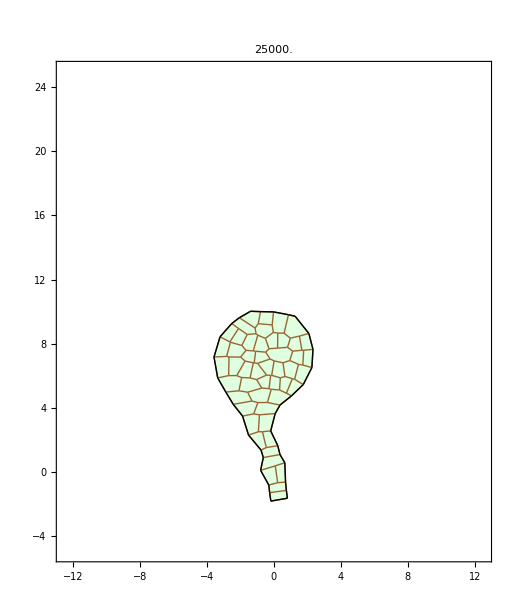

Simulation Completed at t = 25000. after 42 cell divisions; Normal Exit. CPU: 491.752

```mathematica
SIM=grow[Q,0,25000,
"center"-> cen,
"L1Anticlinal"-> False,
"Intercellular"-> {}, 
"IC"-> myic, 
"Walls"-> False, 
"mumax"-> 1, "mumin"-> 1,"muMaxDegrees"-> 90.0,
"IsotropicGrowth"-> False, 
"kmin"-> 1, "kmax"->1, "kMaxDegrees"-> 0, 
"IsotropicSprings"-> False, 
"TestCase"-> "Grow-Example", 
"IgnoreDivisionRadius"-> Infinity, 
"MaxRadius"-> Infinity, 
"Reactions"-> network, 
"Pumps"-> {},
"Diffusion"-> {}, 
"WallReactions"->{},
"BoundaryConditions"-> {X-> 0}, 
"EdgeVariable"-> ell,
"CellVariable"-> area,
"Growing"-> True,
"Restlength"-> resting,
"k"-> {k, 1&}, 
"mu"-> {μ, .01(.1 + 10*(X[#1][t]+X[#2][t]))&},
"P"-> {P, .01*(.05+100*X[#][t])&}, 
"DivisionModel"-> "Errera",
"Parameters"-> {}, 
"DivisionThreshold"-> 1.1, 
"DivisionSigma"-> 0.10, 
"DivisionVariable"-> area, 
"MinAngleSpread"->135,
"Verbose"-> False, 
"Origin"-> {0, 0}, 
"ShowOptions"-> {Frame-> True,ImageSize-> 512, "CellNumbers"-> False, "EdgeNumbers"-> False, 
PlotRange-> {{-12.5,12.5}, {-5,25}}}
];
```

```mathematica
SIM
```

/Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311

```mathematica
SimAnimate[X, SIM,"Frames"-> 25 , "Values"-> {0, 1.25}, "Colors"-> {White, Blue}, "ShowTime"-> False, BaseStyle-> {FontSize-> 22}, "ImageSize"-> 512, "ImageType"-> "jpg"]
```

Saving files to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Movie-X-10Jun17-1319

ffmpeg -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

ERROR: ffmpeg return code is: 32512

On some versions of Mathematica, the Kernel is unable to locate the correct path execute ffmpeg. You must do this manually:

In a command shell such as bash, terminal, or cmd, change your current working directory to (e.g., with the cd command):
/Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Movie-X-10Jun17-1319
The type the following:
ffmpeg -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'
This should create a movie file /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Movie-X-10Jun17-1319/Movie.mov

{}

```mathematica
LineageAnimate[SIM,"Frames"->25]
```

/Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Lineage.nb

Saving files to /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Movie-Lineage-10Jun17-1330

ffmpeg -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

ERROR: ffmpeg return code is: 32512

On some versions of Mathematica, the Kernel is unable to locate the correct path execute ffmpeg. You must do this manually:

In a command shell such as bash, terminal, or cmd,  change your current working directory to (e.g., with the cd command):
/Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Movie-Lineage-10Jun17-1330
The type the following:
ffmpeg -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'
This should create a movie file /Users/mathman/Cellzilla/Simulations-10-Jun-17/Grow-Example-10Jun17-1311/Movie-Lineage-10Jun17-1330/Movie.mov

{}